# Two Scalar 4

```mathematica
NotebookDirectory[]
```

/home/raj/C_SM/ToySMat1Loop/

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$model="TwoScalar4";
```

```mathematica
<<GenAmp`
```

## Setup

```mathematica
$gaugerules={FAGaugeXi[S[1]]:> 1,FAGaugeXi[S[2]]:> 1};
```

```mathematica
$ampconfigFCFAConvert={ChangeDimension->D,Contract->False,DropSumOver->False,FCFADiracChainJoin->True,FeynAmpDenominatorCombine->True,
FinalSubstitutions->{},InitialSubstitutions->{},List->False,LoopMomenta->{l},LorentzIndexNames->{},Prefactor->1,SMP->False,SUNFIndexNames->{},
SUNIndexNames->{},TransversePolarizationVectors->{},UndoChiralSplittings->False};
```

## Tadpoles (1->0)

## One Loop P1->0

```mathematica
D1LP=diag[1,{S[1]},{}];
```

loading generic model file /home/raj/C_SM/ToySMat1Loop/models/TwoScalar4/TwoScalar4.gen

> $GenericMixing is OFF

generic model {./models/TwoScalar4/TwoScalar4} initialized

loading classes model file /home/raj/C_SM/ToySMat1Loop/models/TwoScalar4/TwoScalar4.mod

> 2 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 5 vertices

> 8 counterterms of order 1

classes model {./models/TwoScalar4/TwoScalar4} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

## One Loop P2->0

```mathematica
D1LP=diag[1,{S[2]},{}];
```

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

## One Loop (1->1)

## One Loop P1->P1

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 0 Particles insertions

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bc/cc.m, 0 diagrams

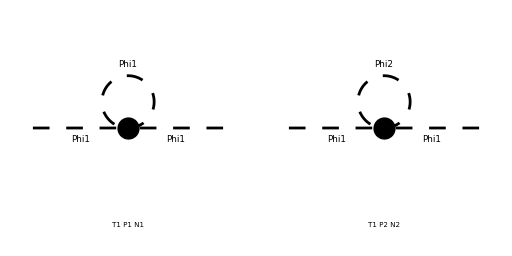

> Top. 1 ac/bc/0.m, 0 diagrams

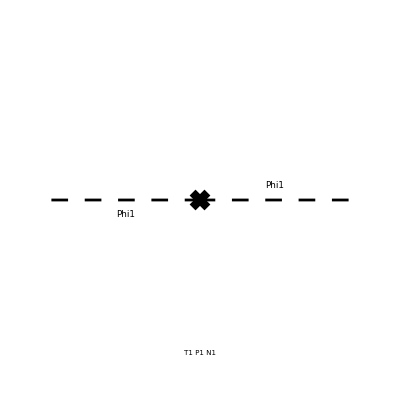

```mathematica
D1LPP=diag[1,{S[1]},{S[1]}];
```

```mathematica
Amp1LPP=D1LPP//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g40)/(32 π^4 (l^2-m1^2))-(ⅈ g22)/(32 π^4 (l^2-m2^2)),-ⅈ (ⅈ p1^2 (ZP-1)-ⅈ m1^2 (Zm1^2 ZP-1))}

```mathematica
Amp1LPPDiv=Amp1LPP//amp1LSimplify[{ZP->1+Nd*dP,Zm1->1+Nd*dm1},{SMP["Delta"],dm1,dP}]
```

-2 dm1 m1^2-dP m1^2+dP p1^2+(Δ g22 m2^2)/(16 π^2)+(Δ g40 m1^2)/(16 π^2)

```mathematica
dsol[1]=Solve[SelectNotFree2[Amp1LPPDiv,p1]==0,dP]//Flatten//Simplify
dSave[dsol[1]];
```

{dP→0}

```mathematica
dsol[2]=Solve[SelectFree2[Amp1LPPDiv/.dSub[dm1],p1]==0,dm1]//Flatten//Simplify
dSave[dsol[2]];
```

{dm1→(Δ (g22 m2^2+g40 m1^2))/(32 π^2 m1^2)}

## One Loop P2->P2

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 0 Particles insertions

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bc/cc.m, 0 diagrams

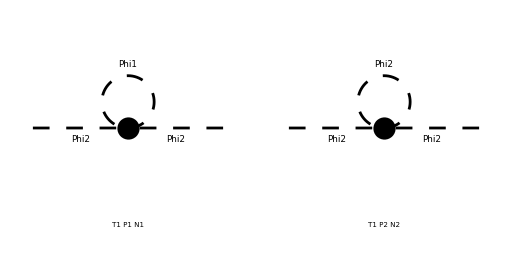

> Top. 1 ac/bc/0.m, 0 diagrams

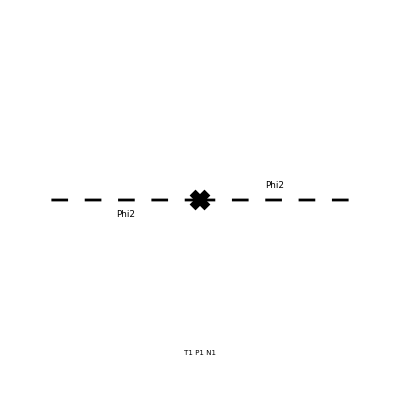

```mathematica
D1LPP=diag[1,{S[2]},{S[2]}];
```

```mathematica
Amp1LPP=D1LPP//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g22)/(32 π^4 (l^2-m1^2))-(ⅈ g04)/(32 π^4 (l^2-m2^2)),-ⅈ (ⅈ p1^2 (ZP-1)-ⅈ m2^2 (Zm2^2 ZP-1))}

```mathematica
Amp1LPPDiv=Amp1LPP//amp1LSimplify[{ZP->1+Nd*dP,Zm2->1+Nd*dm2},{SMP["Delta"],dm2,dP}]
```

-2 dm2 m2^2-dP m2^2+dP p1^2+(Δ g04 m2^2)/(16 π^2)+(Δ g22 m1^2)/(16 π^2)

```mathematica
dsol[3]=Solve[SelectNotFree2[Amp1LPPDiv,p1]==0,dP]//Flatten//Simplify
dSave[dsol[3]];
```

{dP→0}

```mathematica
dsol[4]=Solve[SelectFree2[Amp1LPPDiv/.dSub[dm2],p1]==0,dm2]//Flatten//Simplify
dSave[dsol[4]];
```

{dm2→(Δ (g04 m2^2+g22 m1^2))/(32 π^2 m2^2)}

## One Loop P1->P2

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 0 Particles insertions

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bc/cc.m, 0 diagrams

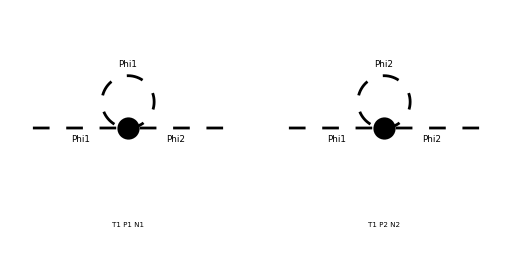

> Top. 1 ac/bc/0.m, 0 diagrams

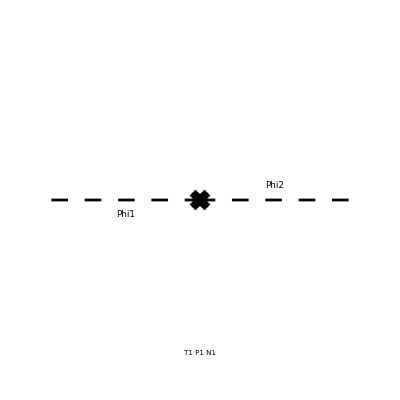

```mathematica
D1LPP=diag[1,{S[1]},{S[2]}];
```

```mathematica
Amp1LPP=D1LPP//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g31)/(32 π^4 (l^2-m1^2))-(ⅈ g13)/(32 π^4 (l^2-m2^2)),-th ZP (m1 Zm1-m2 Zm2) (m1 Zm1+m2 Zm2)}

```mathematica
Amp1LPPDiv=Amp1LPP//amp1LSimplify[{ZP->1+Nd*dP,Zm1->1+Nd*dm1,Zm2->1+Nd*dm2,th->Nd* th},{SMP["Delta"],dm1,dm2,dP,th}]
```

(Δ g13 m2^2)/(16 π^2)+(Δ g31 m1^2)/(16 π^2)+m1^2 (-th)+m2^2 th

```mathematica
dsol[5]=Solve[SelectFree2[Amp1LPPDiv/.dSub[th],p1]==0,th]//Flatten//Simplify
dSave[dsol[5]];
```

{th→(Δ (g13 m2^2+g31 m1^2))/(16 π^2 (m1^2-m2^2))}

## One Loop (2->2)

## One Loop P1 P1->P1 P2

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 3 Particles insertions

> Top. 11: 3 Particles insertions

> Top. 12: 3 Particles insertions

in total: 9 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebe/cfdf/efef.m, 0 diagrams

> Top. 2 aebf/cedf/efef.m, 0 diagrams

> Top. 3 aebf/cfde/efef.m, 0 diagrams

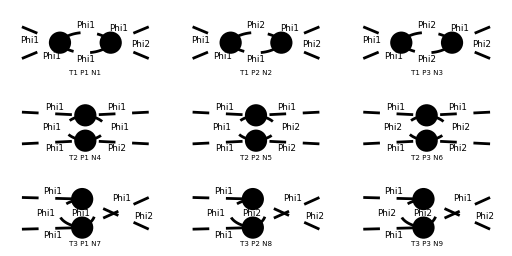

> Top. 1 aebe/cede/0.m, 0 diagrams

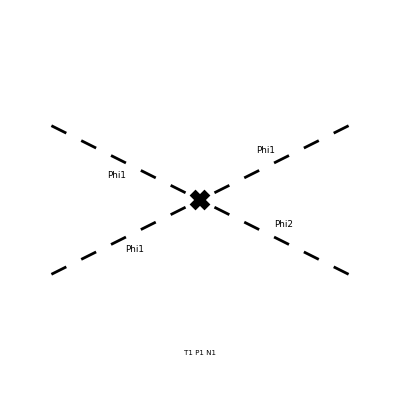

```mathematica
D1LPPPP=diag[1,{S[1],S[1]},{S[1],S[2]}];
```

```mathematica
Amp1LPPPP=D1LPPPP//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 3 Particles amplitudes

> Top. 3: 3 Particles amplitudes

in total: 9 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g13 g22)/(32 π^4 (l^2-m2^2).((l-2 p1)^2-m2^2))-(ⅈ g22 g31)/(16 π^4 (l^2-m1^2).((l-2 p1)^2-m2^2))-(ⅈ g31 g40)/(32 π^4 (l^2-m1^2).((l-2 p1)^2-m1^2))-(ⅈ g13 g22)/(16 π^4 (l^2-m2^2)^2)-(ⅈ g22 g31)/(8 π^4 (l^2-m1^2).(l^2-m2^2))+-(ⅈ g31 g40)/(16 π^4 (l^2-m1^2)^2),3 g22 th Zg22 ZP^2-g31 Zg31 ZP^2+g31-g40 th Zg40 ZP^2}

```mathematica
Amp1LPPPPDiv=Amp1LPPPP//amp1LSimplify[{ZP->1+Nd*dP,Zg40->1+Nd*dg40,Zg22->1+Nd*dg22,Zg04->1+Nd*dg04,Zg31->1+Nd*dg31,Zg13->1+Nd*dg13,th->Nd*th},{SMP["Delta"],dP,th,dg40,dg22,dg04,dg31,dg13}]
```

-dg31 g31-2 dP g31+(3 Δ g13 g22)/(16 π^2)+(3 Δ g22 g31)/(8 π^2)+3 g22 th+(3 Δ g31 g40)/(16 π^2)-g40 th

```mathematica
dsol[6]=Simplify[Flatten[Solve[SelectFree2[Amp1LPPPPDiv/.dSub[dg31],p]==0,dg31]]]
dSave[dsol[6]];
```

{dg31→(Δ (g13 (3 g22 m1^2-g40 m2^2)+g31 (9 g22 m1^2-6 g22 m2^2+2 g40 m1^2-3 g40 m2^2)))/(16 π^2 g31 (m1^2-m2^2))}

## One Loop P1 P2->P2 P2

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 3 Particles insertions

> Top. 11: 3 Particles insertions

> Top. 12: 3 Particles insertions

in total: 9 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebe/cfdf/efef.m, 0 diagrams

> Top. 2 aebf/cedf/efef.m, 0 diagrams

> Top. 3 aebf/cfde/efef.m, 0 diagrams

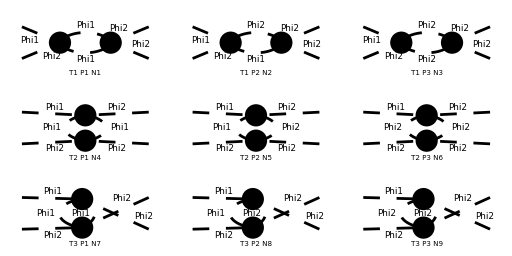

> Top. 1 aebe/cede/0.m, 0 diagrams

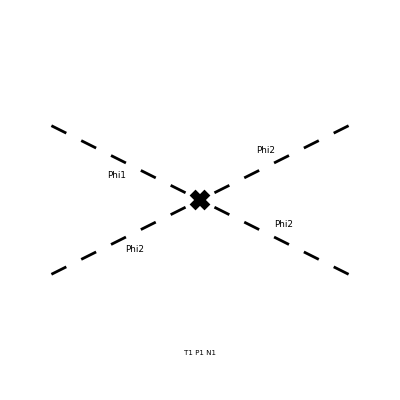

```mathematica
D1LPPPP=diag[1,{S[1],S[2]},{S[2],S[2]}];
```

```mathematica
Amp1LPPPP=D1LPPPP//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 3 Particles amplitudes

> Top. 3: 3 Particles amplitudes

in total: 9 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g04 g13)/(32 π^4 (l^2-m2^2).((l-2 p1)^2-m2^2))-(ⅈ g13 g22)/(16 π^4 (l^2-m1^2).((l-2 p1)^2-m2^2))-(ⅈ g22 g31)/(32 π^4 (l^2-m1^2).((l-2 p1)^2-m1^2))-(ⅈ g04 g13)/(16 π^4 (l^2-m2^2)^2)-(ⅈ g13 g22)/(8 π^4 (l^2-m1^2).(l^2-m2^2))+-(ⅈ g22 g31)/(16 π^4 (l^2-m1^2)^2),g04 th Zg04 ZP^2-g13 Zg13 ZP^2+g13-3 g22 th Zg22 ZP^2}

```mathematica
Amp1LPPPPDiv=Amp1LPPPP//amp1LSimplify[{ZP->1+Nd*dP,Zg40->1+Nd*dg40,Zg22->1+Nd*dg22,Zg04->1+Nd*dg04,Zg31->1+Nd*dg31,Zg13->1+Nd*dg13,th->Nd*th},{SMP["Delta"],dP,th,dg40,dg22,dg04,dg31,dg13}]
```

-dg13 g13-2 dP g13+(3 Δ g04 g13)/(16 π^2)+g04 th+(3 Δ g13 g22)/(8 π^2)+(3 Δ g22 g31)/(16 π^2)-3 g22 th

```mathematica
dsol[7]=Simplify[Flatten[Solve[SelectFree2[Amp1LPPPPDiv/.dSub[dg13],p]==0,dg13]]]
dSave[dsol[7]];
```

{dg13→(Δ (3 g04 g13 m1^2-2 g04 g13 m2^2+g04 g31 m1^2+6 g13 g22 m1^2-9 g13 g22 m2^2-3 g22 g31 m2^2))/(16 π^2 g13 (m1^2-m2^2))}

## One Loop P1 P1->P1 P1

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 3 Particles insertions

> Top. 11: 3 Particles insertions

> Top. 12: 3 Particles insertions

in total: 9 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebe/cfdf/efef.m, 0 diagrams

> Top. 2 aebf/cedf/efef.m, 0 diagrams

> Top. 3 aebf/cfde/efef.m, 0 diagrams

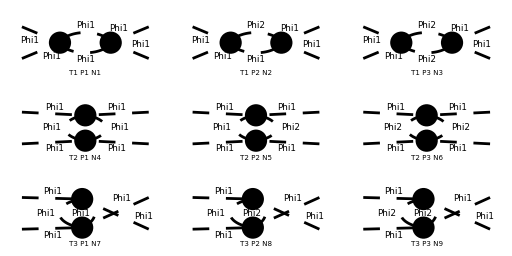

> Top. 1 aebe/cede/0.m, 0 diagrams

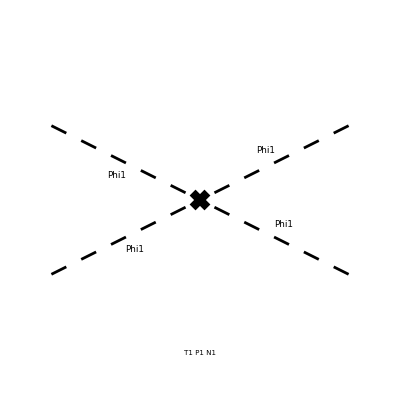

```mathematica
D1LPPPP=diag[1,{S[1],S[1]},{S[1],S[1]}];
```

```mathematica
Amp1LPPPP=D1LPPPP//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 3 Particles amplitudes

> Top. 3: 3 Particles amplitudes

in total: 9 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g22^2)/(32 π^4 (l^2-m2^2).((l-2 p1)^2-m2^2))-(ⅈ g31^2)/(16 π^4 (l^2-m1^2).((l-2 p1)^2-m2^2))-(ⅈ g40^2)/(32 π^4 (l^2-m1^2).((l-2 p1)^2-m1^2))+-(ⅈ g22^2)/(16 π^4 (l^2-m2^2)^2)-(ⅈ g31^2)/(8 π^4 (l^2-m1^2).(l^2-m2^2))-(ⅈ g40^2)/(16 π^4 (l^2-m1^2)^2),4 g31 th Zg31 ZP^2-g40 Zg40 ZP^2+g40}

```mathematica
Amp1LPPPPDiv=Amp1LPPPP//amp1LSimplify[{ZP->1+Nd*dP,Zg40->1+Nd*dg40,Zg22->1+Nd*dg22,Zg04->1+Nd*dg04,Zg31->1+Nd*dg31,Zg13->1+Nd*dg13,th->Nd*th},{SMP["Delta"],dP,th,dg40,dg22,dg04,dg31,dg13}]
```

-dg40 g40-2 dP g40+(3 Δ g22^2)/(16 π^2)+(3 Δ g31^2)/(8 π^2)+4 g31 th+(3 Δ g40^2)/(16 π^2)

```mathematica
dsol[8]=Simplify[Flatten[Solve[SelectFree2[Amp1LPPPPDiv/.dSub[dg40],p]==0,dg40]]]
dSave[dsol[8]];
```

{dg40→(Δ (4 g13 g31 m2^2+3 g22^2 (m1^2-m2^2)+2 g31^2 (5 m1^2-3 m2^2)+3 g40^2 (m1^2-m2^2)))/(16 π^2 g40 (m1^2-m2^2))}

## One Loop P2 P2->P2 P2

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 3 Particles insertions

> Top. 11: 3 Particles insertions

> Top. 12: 3 Particles insertions

in total: 9 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebe/cfdf/efef.m, 0 diagrams

> Top. 2 aebf/cedf/efef.m, 0 diagrams

> Top. 3 aebf/cfde/efef.m, 0 diagrams

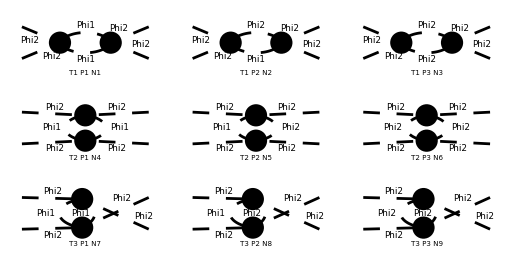

> Top. 1 aebe/cede/0.m, 0 diagrams

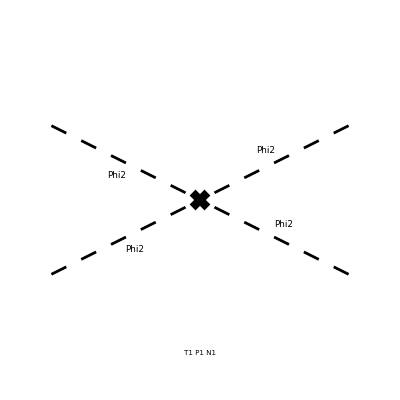

```mathematica
D1LPPPP=diag[1,{S[2],S[2]},{S[2],S[2]}];
```

```mathematica
Amp1LPPPP=D1LPPPP//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 3 Particles amplitudes

> Top. 3: 3 Particles amplitudes

in total: 9 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g04^2)/(32 π^4 (l^2-m2^2).((l-2 p1)^2-m2^2))-(ⅈ g13^2)/(16 π^4 (l^2-m1^2).((l-2 p1)^2-m2^2))-(ⅈ g22^2)/(32 π^4 (l^2-m1^2).((l-2 p1)^2-m1^2))+-(ⅈ g04^2)/(16 π^4 (l^2-m2^2)^2)-(ⅈ g13^2)/(8 π^4 (l^2-m1^2).(l^2-m2^2))-(ⅈ g22^2)/(16 π^4 (l^2-m1^2)^2),-g04 Zg04 ZP^2+g04-4 g13 th Zg13 ZP^2}

```mathematica
Amp1LPPPPDiv=Amp1LPPPP//amp1LSimplify[{ZP->1+Nd*dP,Zg40->1+Nd*dg40,Zg22->1+Nd*dg22,Zg04->1+Nd*dg04,Zg31->1+Nd*dg31,Zg13->1+Nd*dg13,th->Nd*th},{SMP["Delta"],dP,th,dg40,dg22,dg04,dg31,dg13}]
```

-dg04 g04-2 dP g04+(3 Δ g04^2)/(16 π^2)+(3 Δ g13^2)/(8 π^2)-4 g13 th+(3 Δ g22^2)/(16 π^2)

```mathematica
dsol[9]=Simplify[Flatten[Solve[SelectFree2[Amp1LPPPPDiv/.dSub[dg04],p]==0,dg04]]]
dSave[dsol[9]];
```

{dg04→(Δ (3 g04^2 (m1^2-m2^2)+2 g13^2 (3 m1^2-5 m2^2)-4 g13 g31 m1^2+3 g22^2 (m1^2-m2^2)))/(16 π^2 g04 (m1^2-m2^2))}

## One Loop P1 P1->P2 P2

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 3 Particles insertions

> Top. 11: 3 Particles insertions

> Top. 12: 3 Particles insertions

in total: 9 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebe/cfdf/efef.m, 0 diagrams

> Top. 2 aebf/cedf/efef.m, 0 diagrams

> Top. 3 aebf/cfde/efef.m, 0 diagrams

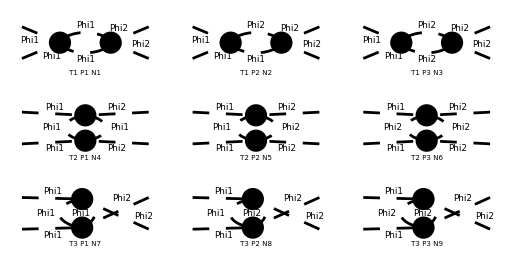

> Top. 1 aebe/cede/0.m, 0 diagrams

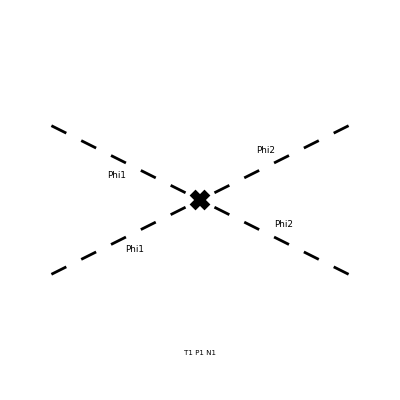

```mathematica
D1LPPPP=diag[1,{S[1],S[1]},{S[2],S[2]}];
```

```mathematica
Amp1LPPPP=D1LPPPP//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 3 Particles amplitudes

> Top. 3: 3 Particles amplitudes

in total: 9 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g04 g22)/(32 π^4 (l^2-m2^2).((l-2 p1)^2-m2^2))-(ⅈ g13 g31)/(16 π^4 (l^2-m1^2).((l-2 p1)^2-m2^2))-(ⅈ g22 g40)/(32 π^4 (l^2-m1^2).((l-2 p1)^2-m1^2))+-(ⅈ g13^2)/(16 π^4 (l^2-m2^2)^2)-(ⅈ g22^2)/(8 π^4 (l^2-m1^2).(l^2-m2^2))-(ⅈ g31^2)/(16 π^4 (l^2-m1^2)^2),2 g13 th Zg13 ZP^2-g22 Zg22 ZP^2+4 g22-2 g31 th Zg31 ZP^2}

```mathematica
Amp1LPPPPDiv=Amp1LPPPP//amp1LSimplify[{ZP->1+Nd*dP,Zg40->1+Nd*dg40,Zg22->1+Nd*dg22,Zg04->1+Nd*dg04,Zg31->1+Nd*dg31,Zg13->1+Nd*dg13,th->Nd*th},{SMP["Delta"],dP,th,dg40,dg22,dg04,dg31,dg13}]
```

-dg22 g22-2 dP g22+(Δ g04 g22)/(16 π^2)+(Δ g13^2)/(8 π^2)+(Δ g13 g31)/(8 π^2)+2 g13 th+(Δ g22^2)/(4 π^2)+(Δ g22 g40)/(16 π^2)+(Δ g31^2)/(8 π^2)-2 g31 th

```mathematica
dsol[10]=Simplify[Flatten[Solve[SelectFree2[Amp1LPPPPDiv/.dSub[dg22],p]==0,dg22]]]
dSave[dsol[10]];
```

{dg22→1/(16 π^2 g22 (m1^2-m2^2))Δ (g04 g22 (m1^2-m2^2)+2 g13^2 m1^2+4 g13 g31 (m1^2-m2^2)+4 g22^2 m1^2-4 g22^2 m2^2+g22 g40 m1^2-g22 g40 m2^2-2 g31^2 m2^2)}

## Final answers

```mathematica
dvalues//Simplify
```

{dm1→(Δ (g22 m2^2+g40 m1^2))/(32 π^2 m1^2),dP→0,dm2→(Δ (g04 m2^2+g22 m1^2))/(32 π^2 m2^2),th→(Δ (g13 m2^2+g31 m1^2))/(16 π^2 (m1^2-m2^2)),dg31→(Δ (g13 (3 g22 m1^2-g40 m2^2)+g31 (9 g22 m1^2-6 g22 m2^2+2 g40 m1^2-3 g40 m2^2)))/(16 π^2 g31 (m1^2-m2^2)),dg13→(Δ (3 g04 g13 m1^2-2 g04 g13 m2^2+g04 g31 m1^2+6 g13 g22 m1^2-9 g13 g22 m2^2-3 g22 g31 m2^2))/(16 π^2 g13 (m1^2-m2^2)),dg40→(Δ (4 g13 g31 m2^2+3 g22^2 (m1^2-m2^2)+2 g31^2 (5 m1^2-3 m2^2)+3 g40^2 (m1^2-m2^2)))/(16 π^2 g40 (m1^2-m2^2)),dg04→(Δ (3 g04^2 (m1^2-m2^2)+2 g13^2 (3 m1^2-5 m2^2)-4 g13 g31 m1^2+3 g22^2 (m1^2-m2^2)))/(16 π^2 g04 (m1^2-m2^2)),dg22→(Δ (g04 g22 (m1^2-m2^2)+2 g13^2 m1^2+4 g13 g31 (m1^2-m2^2)+4 g22^2 m1^2-4 g22^2 m2^2+g22 g40 m1^2-g22 g40 m2^2-2 g31^2 m2^2))/(16 π^2 g22 (m1^2-m2^2))}

### Starting with the same initial parameter g

```mathematica
ParamConfig1=dvalues/.{g04->g,g40->g,g22->g,g13->g,g31->g}//Simplify
```

{dm1→(Δ g (m1^2+m2^2))/(32 π^2 m1^2),dP→0,dm2→(Δ g (m1^2+m2^2))/(32 π^2 m2^2),th→(Δ g (m1^2+m2^2))/(16 π^2 (m1^2-m2^2)),dg31→(Δ g (7 m1^2-5 m2^2))/(8 π^2 (m1^2-m2^2)),dg13→(Δ g (5 m1^2-7 m2^2))/(8 π^2 (m1^2-m2^2)),dg40→(Δ g (2 m1^2-m2^2))/(2 π^2 (m1^2-m2^2)),dg04→(Δ g (m1^2-2 m2^2))/(2 π^2 (m1^2-m2^2)),dg22→(3 Δ g)/(4 π^2)}

### Adding ϕ_1->-ϕ_1 and ϕ_2->-ϕ_2 symmetry

```mathematica
ParamConfig2=dvalues/.{g04->g,g40->g,g22->g/3,g13->0,g31->0}//Simplify
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0 ComplexInfinity Δ)/((m1^2-m2^2) π^2) encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0 ComplexInfinity Δ)/((m1^2-m2^2) π^2) encountered.

{dm1→(Δ g (3 m1^2+m2^2))/(96 π^2 m1^2),dP→0,dm2→(Δ g (m1^2+3 m2^2))/(96 π^2 m2^2),th→0,dg31→Indeterminate,dg13→Indeterminate,dg40→(5 Δ g)/(24 π^2),dg04→(5 Δ g)/(24 π^2),dg22→(5 Δ g)/(24 π^2)}

### Similar to complex scalar theory (only need to renormalize the mass and Φ^4 coupling)

```mathematica
ParamConfig3=ParamConfig2/.{m1->m,m2->m}//Simplify
```

{dm1→(Δ g)/(24 π^2),dP→0,dm2→(Δ g)/(24 π^2),th→0,dg31→Indeterminate,dg13→Indeterminate,dg40→(5 Δ g)/(24 π^2),dg04→(5 Δ g)/(24 π^2),dg22→(5 Δ g)/(24 π^2)}